## Lab07 - Bonus

```mathematica
data={{6.25,0.0},{6.001765667929582,0.4991670832341408},{5.278004317051997,0.9933466539753061},{4.13971935999042,1.477601033306698},{2.6826721590673235,1.9470917115432527},{1.0290638906736893,2.397127693021015},{-3.7234679805828397,3.586780454497614},{-4.804363328451665,3.916634548137417},{-5.4701460286861545,4.207354924039483},{-5.6730252461135064,4.456036800307177},{-5.4055342260972905,4.660195429836132},{-4.700772462711884,4.817790927085965},{-3.62908203253932,4.927248649942301},{-2.2914696179044554,4.987474933020272},{-0.810373552546205,4.997868015207525},{0.6813909728405793,4.958324052262343},{2.05251635929549,4.869238154390976},{3.1848542843027783,4.731500438437072},{3.983796907172315,4.546487134128409},{4.386467155241201,4.316046833244369},{4.366996872319622,4.0424820190979505},{3.938434841957967,3.7285260608836},{3.1511303019605785,3.377315902755753},
{2.087754321004162,2.992360720519782},{0.8554229419387158,2.577506859107321},{-0.42435467375067093,2.136899401169149},{-1.6269859224456151,1.6749407507795233},{-2.63633383181035,1.19624664606991},
{-3.3554384511104276,0.7056000402993361},{-3.715449005983995,0.20790331216645247},{-3.681958130522893,-0.2918707171379004},{-3.258165023178643,-0.7887284707162433},{-2.4845813971987143,-1.2777055101341583},{-1.435306822050832,-1.7539161384480992},{-0.21121038911135578,-2.2126022164742625},{1.0693642937964811,-2.649180704542467},{2.281529134967273,-3.0592894547135963},{3.3054259689726977,-3.4388307959198707},{4.037394751401694,-3.7840124765396412},{6.399719513203253,-4.091385555322054},{4.348062109859167,-4.357878862067941},
{3.8759001316492907,-4.580829683747274},{3.0155535206251787,-4.758010369447581},{1.8356904891936137,-4.887650588325485},{0.43551986299002976,-4.968455018167322},{-1.0638243785898849,-4.999616287820504},{-2.529946600811446,-4.9808230441792025},{-3.8309547730765376,-4.912263063121662},{-4.847278975639672,-4.794621373315692},{-5.482485967105465,-4.629073411638661},{-5.672118447703113,-4.417273278600765},{-5.389760456496705,-4.161337211119504},{-4.649774834880334,-3.8638224377799357},{-3.5064531650285042,-3.5277016278519597},{-2.0496368572833727,-3.1563331893616042},{-0.39718177268071464,-2.753427712988188},{1.3150800368523572,-2.323010897068783},{2.9450042957329634,-1.8693833241511801},{4.3564009896360165,-1.3970774909946293},{5.4308248157476635,-0.9108125213604751},{6.07785134254383,-0.41544701408748197}
};
```

```mathematica
MatrixForm[data];
```

```mathematica
data = Join[data, {{6.25, 0.}}]
```

{{6.25,0.},{6.00177,0.499167},{5.278,0.993347},{4.13972,1.4776},{2.68267,1.94709},{1.02906,2.39713},{-3.72347,3.58678},{-4.80436,3.91663},{-5.47015,4.20735},{-5.67303,4.45604},{-5.40553,4.6602},{-4.70077,4.81779},{-3.62908,4.92725},{-2.29147,4.98747},{-0.810374,4.99787},{0.681391,4.95832},{2.05252,4.86924},{3.18485,4.7315},{3.9838,4.54649},{4.38647,4.31605},{4.367,4.04248},{3.93843,3.72853},{3.15113,3.37732},{2.08775,2.99236},{0.855423,2.57751},{-0.424355,2.1369},{-1.62699,1.67494},{-2.63633,1.19625},{-3.35544,0.7056},{-3.71545,0.207903},{-3.68196,-0.291871},{-3.25817,-0.788728},{-2.48458,-1.27771},{-1.43531,-1.75392},{-0.21121,-2.2126},{1.06936,-2.64918},{2.28153,-3.05929},{3.30543,-3.43883},{4.03739,-3.78401},{6.39972,-4.09139},{4.34806,-4.35788},{3.8759,-4.58083},{3.01555,-4.75801},{1.83569,-4.88765},{0.43552,-4.96846},{-1.06382,-4.99962},{-2.52995,-4.98082},{-3.83095,-4.91226},{-4.84728,-4.79462},{-5.48249,-4.62907},{-5.67212,-4.41727},{-5.38976,-4.16134},{-4.64977,-3.86382},{-3.50645,-3.5277},{-2.04964,-3.15633},{-0.397182,-2.75343},{1.31508,-2.32301},{2.945,-1.86938},{4.3564,-1.39708},{5.43082,-0.910813},{6.07785,-0.415447},{6.25,0.}}

```mathematica
dataT = Transpose[data]
```

{{6.25,6.00177,5.278,4.13972,2.68267,1.02906,-3.72347,-4.80436,-5.47015,-5.67303,-5.40553,-4.70077,-3.62908,-2.29147,-0.810374,0.681391,2.05252,3.18485,3.9838,4.38647,4.367,3.93843,3.15113,2.08775,0.855423,-0.424355,-1.62699,-2.63633,-3.35544,-3.71545,-3.68196,-3.25817,-2.48458,-1.43531,-0.21121,1.06936,2.28153,3.30543,4.03739,6.39972,4.34806,3.8759,3.01555,1.83569,0.43552,-1.06382,-2.52995,-3.83095,-4.84728,-5.48249,-5.67212,-5.38976,-4.64977,-3.50645,-2.04964,-0.397182,1.31508,2.945,4.3564,5.43082,6.07785,6.25},{0.,0.499167,0.993347,1.4776,1.94709,2.39713,3.58678,3.91663,4.20735,4.45604,4.6602,4.81779,4.92725,4.98747,4.99787,4.95832,4.86924,4.7315,4.54649,4.31605,4.04248,3.72853,3.37732,2.99236,2.57751,2.1369,1.67494,1.19625,0.7056,0.207903,-0.291871,-0.788728,-1.27771,-1.75392,-2.2126,-2.64918,-3.05929,-3.43883,-3.78401,-4.09139,-4.35788,-4.58083,-4.75801,-4.88765,-4.96846,-4.99962,-4.98082,-4.91226,-4.79462,-4.62907,-4.41727,-4.16134,-3.86382,-3.5277,-3.15633,-2.75343,-2.32301,-1.86938,-1.39708,-0.910813,-0.415447,0.}}

```mathematica
xData = dataT[[1]]
```

{6.25,6.00177,5.278,4.13972,2.68267,1.02906,-3.72347,-4.80436,-5.47015,-5.67303,-5.40553,-4.70077,-3.62908,-2.29147,-0.810374,0.681391,2.05252,3.18485,3.9838,4.38647,4.367,3.93843,3.15113,2.08775,0.855423,-0.424355,-1.62699,-2.63633,-3.35544,-3.71545,-3.68196,-3.25817,-2.48458,-1.43531,-0.21121,1.06936,2.28153,3.30543,4.03739,6.39972,4.34806,3.8759,3.01555,1.83569,0.43552,-1.06382,-2.52995,-3.83095,-4.84728,-5.48249,-5.67212,-5.38976,-4.64977,-3.50645,-2.04964,-0.397182,1.31508,2.945,4.3564,5.43082,6.07785,6.25}

```mathematica
yData = dataT[[2]]
```

{0.,0.499167,0.993347,1.4776,1.94709,2.39713,3.58678,3.91663,4.20735,4.45604,4.6602,4.81779,4.92725,4.98747,4.99787,4.95832,4.86924,4.7315,4.54649,4.31605,4.04248,3.72853,3.37732,2.99236,2.57751,2.1369,1.67494,1.19625,0.7056,0.207903,-0.291871,-0.788728,-1.27771,-1.75392,-2.2126,-2.64918,-3.05929,-3.43883,-3.78401,-4.09139,-4.35788,-4.58083,-4.75801,-4.88765,-4.96846,-4.99962,-4.98082,-4.91226,-4.79462,-4.62907,-4.41727,-4.16134,-3.86382,-3.5277,-3.15633,-2.75343,-2.32301,-1.86938,-1.39708,-0.910813,-0.415447,0.}

```mathematica
Length[xData]
```

62

```mathematica
xFunc = Interpolation[xData, Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
yFunc = Interpolation[yData, Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
func[t_] = {xFunc[t], yFunc[t]}
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

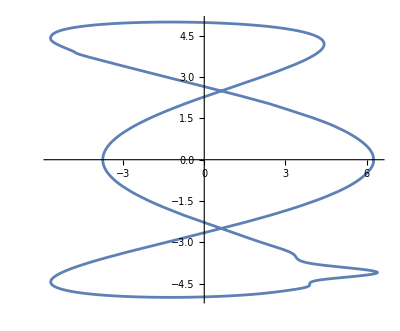

```mathematica
plot = ParametricPlot[func[t], {t, 1, Length[xData]}, Exclusions->None]
```

```mathematica
colourList = Table[RandomColor[], {i,10}]
```

{RGBColor[0.39423014104186405, 0.8270567681850132, 0.12911922479015403],RGBColor[0.5529562151861687, 0.14422501569121216, 0.3986162279969361],RGBColor[0.010499964710044996, 0.17202645315999798, 0.07297464578567991],RGBColor[0.1763458097983186, 0.7472849673303159, 0.6306739491975326],RGBColor[0.6779592363788798, 0.9485031903260364, 0.28257861298662923],RGBColor[0.3936065872256598, 0.9859292362138936, 0.9894385370214529],RGBColor[0.5430115178328128, 0.8719054069929932, 0.04366069863212618],RGBColor[0.18663635007739932, 0.040525101671589514, 0.25358865148611365],RGBColor[0.3851104185682177, 0.3942609964467627, 0.6975951644063514],RGBColor[0.6879473918804466, 0.1196320037869869, 0.9301461562767617]}

```mathematica
objectShape[t_, colour_, sides_] := {colour, RegularPolygon[{0,0}, 1, sides]}
```

```mathematica
objectMenu = PopupMenu[Dynamic[sides], {3 -> "Triangle", 4 -> "Square", 5 -> "Pentagon"}]
```

```mathematica
objectRotate[t_, colour_,sides_, angle_] := GeometricTransformation[objectShape[t, colour, sides], Composition[TranslationTransform[func[t]], RotationTransform[angle]]]
```

```mathematica
objectRotatePlot[t_, colour_,sides_, angle_] := Graphics[objectRotate[t, colour, sides, angle],Axes->True]
```

```mathematica
showBoth[t_, colour_,sides_, angle_] := Show[{plot, objectRotatePlot[t, colour, sides, angle]}]
```

```mathematica
Manipulate[showBoth[t, colour,sides, angle ], {angle, 0,2Pi}, {t, 1,Length[xData]},{colour, colourList}]
```